```mathematica
Quit[]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\Jieyu You\Google Drive\multi atom

```mathematica
atom=2;(*num of atoms*)
dim=2^atom;(*dimension in Hilbert space*)
 xij[i_,j_]:=ReplacePart[ConstantArray[0,{dim,dim}],{i,j}->1]
ithzero[digit_,kth_]/;kth≤ digit:=Tuples[ReplacePart[Table[{1,0},{digit}],kth->{0}]];
Do[σ[i,1]=Sum[xij[2^atom+1-(x+2^(atom-i)+1),2^atom+1-(x+1)]Boole[MemberQ[ithzero[atom,i],IntegerDigits[x,2,atom]]],{x,0,2^atom-1}],{i,1,atom}];
Do[σ[i,0]=Transpose[σ[i,1]],{i,1,atom}];
(*mapping: eeee->1111->2^4-1, i is the ith from the left*)
ρ[t_]:=Table[a[i,j][t],{i,dim},{j,dim}]
slnn=Flatten[Table[a[i,j][t],{i,dim},{j,dim}]];
(*basis:a1a2a3,a1a2b3,a1b2a3,a1b2b3,b1a2a3,b1a2b3,b1b2a3,b1b2b3*)
cij[t_]:=Table[c[i,j][t],{i,dim},{j,dim}];
slnc=Flatten[Table[c[i,j][t],{i,dim},{j,dim}]];
init=DiagonalMatrix[Append[ConstantArray[0,dim-1],1]];
λ0=1;k0=2Pi/λ0;
rr=0.5;
sh=Sinh[rr];
ch=Cosh[rr];
ΩR=4;
r[5]=1 λ0;
r[4]=0.5λ0;
r[3]=0 λ0;
r[2]=0.25λ0;
r[1]=-0.25λ0;
cut=100Pi;
Do[θ=x Pi/2;
(*independent*)
Λ[i_,j_]:=(*Λ[i,j]=*)0.5Sin[k0 Abs[r[i]-r[j]] ]KroneckerDelta[i,j];
γ[i_,j_]:=(*γ[i,j]=*)Cos[k0 Abs[r[j]-r[i]] ]KroneckerDelta[i,j];
γp[i_,j_]:=(*γp[i,j]=*)Cos[k0(r[i]+r[j])]KroneckerDelta[i,j];
V=0.5ΩR Sum[Exp[-I θ]Exp[-I k0 r[i]]σ[i,0]+Exp[I θ]Exp[I k0 r[i]]σ[i,1],{i,1,atom}];
SQ=0.5sh ch Sum[γp[i,j](ρ[t].σ[i,α].σ[j,α]+σ[i,α].σ[j,α].ρ[t]-2σ[j,α].ρ[t].σ[i,α]),{i,1,atom},{j,1,atom},{α,0,1}]-0.5(sh^2+1)Sum[γ[i,j](ρ[t].σ[i,1].σ[j,0]+σ[i,1].σ[j,0].ρ[t]-2σ[j,0].ρ[t].σ[i,1]),{i,1,atom},{j,1,atom}]-0.5 sh^2Sum[γ[i,j](ρ[t].σ[i,0].σ[j,1]+σ[i,0].σ[j,1].ρ[t]-2σ[j,1].ρ[t].σ[i,0]),{i,1,atom},{j,1,atom}]-I Sum[Λ[i,j](σ[i,1].σ[j,0].ρ[t]-ρ[t].σ[i,1].σ[j,0]),{i,1,atom},{j,1,atom}];
SQc=0.5sh ch Sum[γp[i,j]( cij[t].σ[i,α].σ[j,α]+σ[i,α].σ[j,α]. cij[t]-2σ[j,α]. cij[t].σ[i,α]),{i,1,atom},{j,1,atom},{α,0,1}]-0.5(sh^2+1)Sum[γ[i,j]( cij[t].σ[i,1].σ[j,0]+σ[i,1].σ[j,0]. cij[t]-2σ[j,0]. cij[t].σ[i,1]),{i,1,atom},{j,1,atom}]-0.5 sh^2Sum[γ[i,j]( cij[t].σ[i,0].σ[j,1]+σ[i,0].σ[j,1]. cij[t]-2σ[j,1]. cij[t].σ[i,0]),{i,1,atom},{j,1,atom}]-I Sum[Λ[i,j](σ[i,1].σ[j,0]. cij[t]- cij[t].σ[i,1].σ[j,0]),{i,1,atom},{j,1,atom}];
DR=-I (V.ρ[t]-ρ[t].V);
DRc=-I (V.cij[t]-cij[t].V);
solsq=NDSolve[{ρ'[t]==SQ+DR,ρ[0]==init},slnn,{t,0,5000}];
initc=Sum[σ[i,0],{i,1,atom}].(ρ[t]/.solsq/.t->5000)[[1]];
solc=NDSolve[{cij'[t]==SQc+DRc,cij[0]==initc},slnc,{t,0,5000}];

ss=Tr[((cij[t]/.solc)[[1]].Sum[σ[i,1],{i,1,atom}])]/.t->5000;
dt=0.01;
spec=Flatten[Re[InverseFourier[Table[Tr[((cij[t]/.solc)[[1]].Sum[σ[i,1],{i,1,atom}])]-ss,{t,0,cut,dt}]]]];
p=IntegerPart[cut/dt/2];
specc=ConstantArray[0,2p];
spec=spec/spec[[1]];
specc[[1;;p]]=spec[[p+1;;2p]];
specc[[p+1;;2p]]=spec[[1;;p]];
psd[x]=specc;
plotpsd[x]=ListLinePlot[specc,DataRange->{-Pi 1/dt,Pi 1/dt},PlotRange->{{-10,10},{-0.05,1.5}},PlotLegends->"vac",PlotStyle->{Blue,Dashed}];

(*interaction*)
Λi[i_,j_]:=(*Λ[i,j]=*)0.5Sin[k0 Abs[r[i]-r[j]] ];
γi[i_,j_]:=(*γ[i,j]=*)Cos[k0 Abs[r[j]-r[i]] ];
γpi[i_,j_]:=(*γp[i,j]=*)Cos[k0(r[i]+r[j])];
V=0.5ΩR Sum[Exp[-I θ]Exp[-I k0 r[i]]σ[i,0]+Exp[I θ]Exp[I k0 r[i]]σ[i,1],{i,1,atom}];
SQi=0.5sh ch Sum[γpi[i,j](ρ[t].σ[i,α].σ[j,α]+σ[i,α].σ[j,α].ρ[t]-2σ[j,α].ρ[t].σ[i,α]),{i,1,atom},{j,1,atom},{α,0,1}]-0.5(sh^2+1)Sum[γi[i,j](ρ[t].σ[i,1].σ[j,0]+σ[i,1].σ[j,0].ρ[t]-2σ[j,0].ρ[t].σ[i,1]),{i,1,atom},{j,1,atom}]-0.5 sh^2Sum[γi[i,j](ρ[t].σ[i,0].σ[j,1]+σ[i,0].σ[j,1].ρ[t]-2σ[j,1].ρ[t].σ[i,0]),{i,1,atom},{j,1,atom}]-I Sum[Λi[i,j](σ[i,1].σ[j,0].ρ[t]-ρ[t].σ[i,1].σ[j,0]),{i,1,atom},{j,1,atom}];
SQci=0.5sh ch Sum[γpi[i,j]( cij[t].σ[i,α].σ[j,α]+σ[i,α].σ[j,α]. cij[t]-2σ[j,α]. cij[t].σ[i,α]),{i,1,atom},{j,1,atom},{α,0,1}]-0.5(sh^2+1)Sum[γi[i,j]( cij[t].σ[i,1].σ[j,0]+σ[i,1].σ[j,0]. cij[t]-2σ[j,0]. cij[t].σ[i,1]),{i,1,atom},{j,1,atom}]-0.5 sh^2Sum[γi[i,j]( cij[t].σ[i,0].σ[j,1]+σ[i,0].σ[j,1]. cij[t]-2σ[j,1]. cij[t].σ[i,0]),{i,1,atom},{j,1,atom}]-I Sum[Λi[i,j](σ[i,1].σ[j,0]. cij[t]- cij[t].σ[i,1].σ[j,0]),{i,1,atom},{j,1,atom}];
DRi=-I (V.ρ[t]-ρ[t].V);
DRci=-I (V.cij[t]-cij[t].V);
solsqi=NDSolve[{ρ'[t]==SQi+DRi,ρ[0]==init},slnn,{t,0,5000}];
initci=Sum[σ[i,0],{i,1,atom}].(ρ[t]/.solsqi/.t->5000)[[1]];
solci=NDSolve[{cij'[t]==SQci+DRci,cij[0]==initci},slnc,{t,0,5000}];

ssi=Tr[((cij[t]/.solci)[[1]].Sum[σ[i,1],{i,1,atom}])]/.t->5000;
dt=0.01;
speci=Flatten[Re[InverseFourier[Table[Tr[((cij[t]/.solci)[[1]].Sum[σ[i,1],{i,1,atom}])]-ssi,{t,0,cut,dt}]]]];
pi=IntegerPart[cut/dt/2];
specci=ConstantArray[0,2pi];
speci=speci/speci[[1]];
specci[[1;;pi]]=speci[[pi+1;;2pi]];
specci[[pi+1;;2pi]]=speci[[1;;pi]];
psr[x]=specci;
plotpsr[x]=ListLinePlot[specci,DataRange->{-Pi 1/dt,Pi 1/dt},PlotRange->{{-10,10},{-0.05,1.5}},PlotLegends->"vac",PlotStyle->{Green}]

,{x,0,1,1}]
(*Do[Print[Show[plotpsr[x],plotpsd[x]]],{x,0.5,0.9,0.1}]*)
```

```mathematica
2p
```

31414

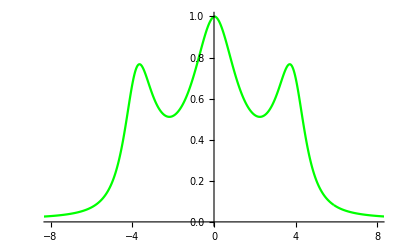

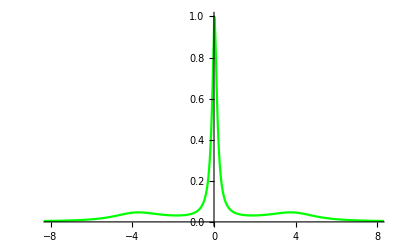

```mathematica
Do[Print[ListLinePlot[psr[x],DataRange->{-Pi 1/dt,Pi 1/dt},PlotRange->{{-8,8},Full},PlotLegends->"vac",PlotStyle->{Green}]],{x,0,1}]
```

```mathematica
Export["0&1.dat",{psr[0],psr[1],psd[0],psd[1]}//Transpose](*r: real, 0: phase=0pi/2*)
```

0&1.dat

```mathematica
psr[0]
```

{0.00174745,0.00174745,0.00174745,0.00174745,0.00174745,0.00174745,0.00174745,0.00174745,31398,0.00174745,0.00174745,0.00174745,0.00174745,0.00174745,0.00174745,0.00174745,0.00174745}
 |  |  |  |

```mathematica
Sinh[0.5]^2
Sinh[1.]^2
```

0.27154

1.3811

```mathematica
Export["x.dat",Range[-Pi 1/dt,Pi 1/dt,2 Pi/(dt 2p)]]
```

x.dat

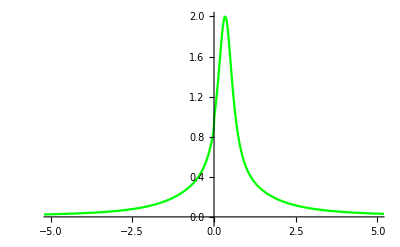

```mathematica
ListLinePlot[psr[1],DataRange->{-Pi 1/dt,Pi 1/dt},PlotRange->{{-5,5},{-0.05,2.}},PlotLegends->"vac",PlotStyle->{Green}]
```

```mathematica
0.5Sin[k0 Abs[r[1]-r[2]] ]
```

0.5